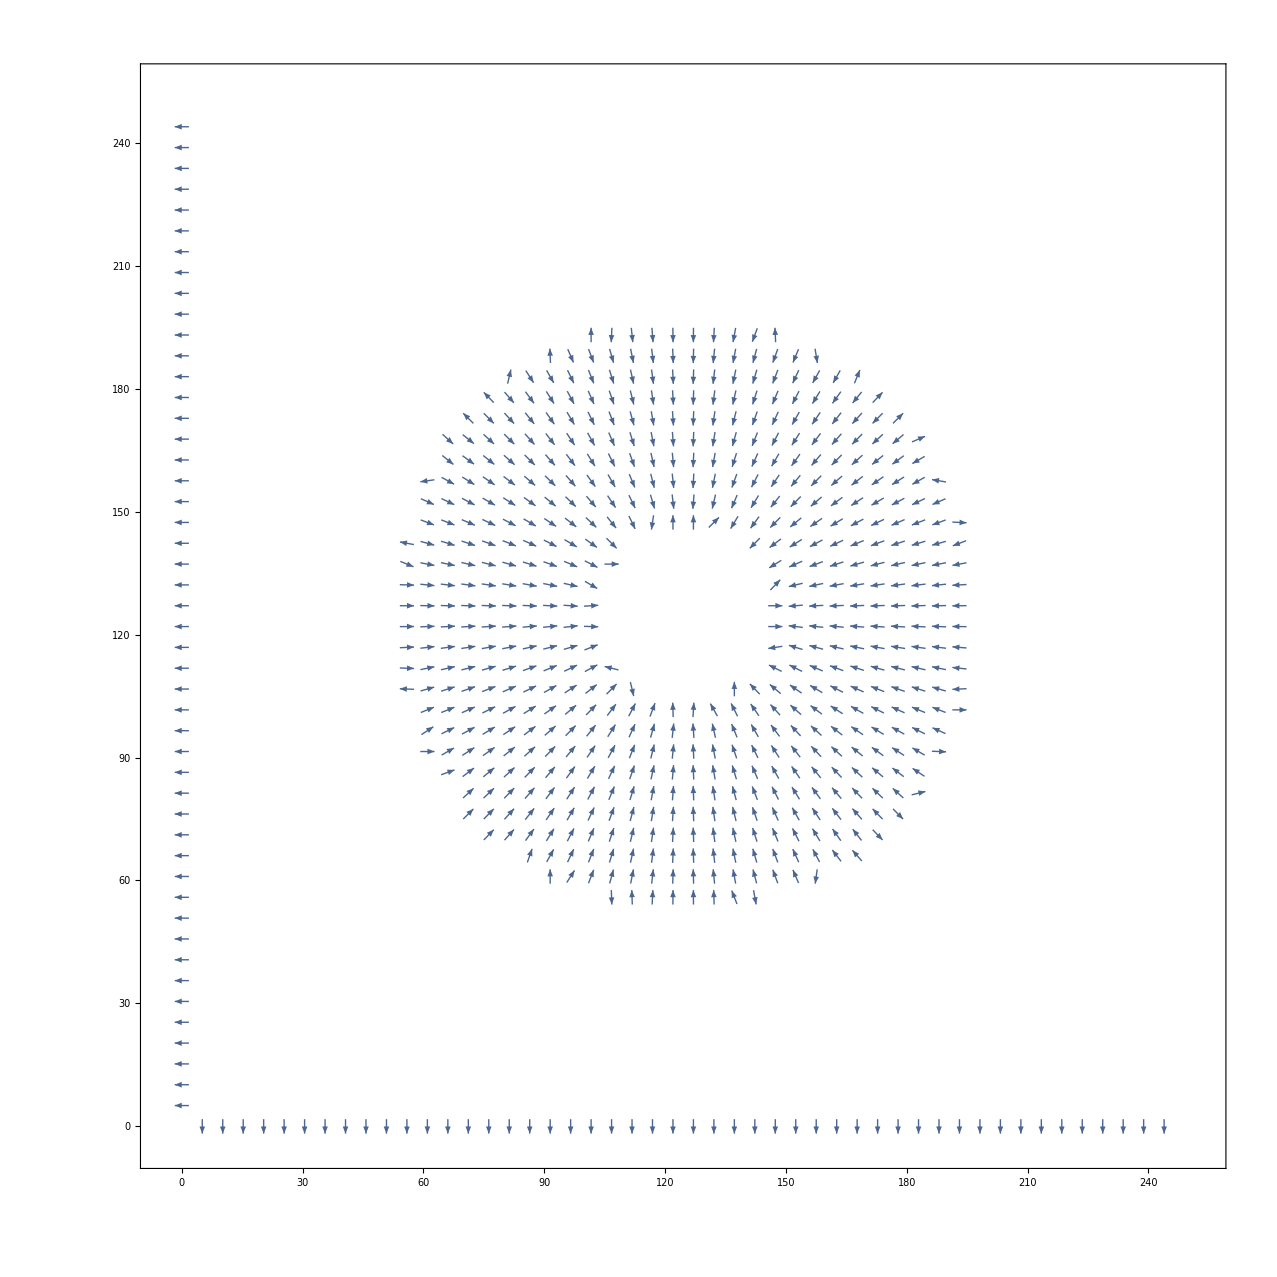

```mathematica
data = Import["electricField.dat","Table"];
coords = data[[All,{1,2}]];
comps = data[[All,{3,4}]];
out = Thread[{coords,comps}];
ListVectorPlot[out,VectorScale->{0.01,Automatic,None},VectorPoints->50]
```